```mathematica
Expand@Sum[ 1/(k!) (n-1)^k,{k,1,Infinity}] Sum[ BernoulliB[k]/(k!) (n-1)^k,{k,0,Infinity}]
```

-1+n

```mathematica
Expand@Sum[ 1/(k!) (n-1)^(k),{k,1,Infinity}] Sum[ BernoulliB[k]/(k!) (n-1)^(k+a),{k,0,Infinity}]
```

(-1+n)^(1+a)

```mathematica
FullSimplify@Sum[ 1/(k!) (n-1)^(k),{k,1,Infinity}]
```

-1+ⅇ^(-1+n)

```mathematica
Expand@Sum[ BernoulliB[k]/(k!) (n-1)^(k+a),{k,0,Infinity}]
```

(-1+n)^(1+a)/(-1+ⅇ^(-1+n))

```mathematica
gg[n_, rr_] :=  (-1)^(rr) Gamma[ rr,0,-Log[n]]/Gamma[rr]
aa[n_, k_] := (-1)^(k+1)/(k-1)! Integrate[ t^(k-1)E^-t, {t,-Log[n],0}]
```

```mathematica
N[Sum[ 1/(k!) gg[20,k] ,{k,1,100}]Sum[ BernoulliB[k]/(k!)gg[20,k],{k,0,120}]]
```

-254.939

```mathematica
Chop@N@gg[10,10]
```

0.00952161

```mathematica
N[Sum[ 1/(k!) gg[20,k] ,{k,1,100}]]
```

49.535

```mathematica
Sum[ 1/(k!) aa[n,k] ,{k,1,Infinity}]
```

$Aborted

```mathematica
N[aa[30,4]]
```

96.2415

```mathematica
Chop@N[gg[30,4]]
```

96.2415

```mathematica
Integrate[Sum[(-1)^(k+1)/(k)  ((-1)^(k+1)/(k-1)!  t^(k-1)E^-t) ,{k,1,Infinity}], {t,-Log[n],0}]
```

ConditionalExpression[-EulerGamma+ExpIntegralEi[Log[n]]-Log[Log[n]],Log[n]>0]

```mathematica
Integrate[Sum[BernoulliB[k]/(k!) ((-1)^(k+1)/(k-1)!  t^(k-1)E^-t) ,{k,0,Infinity}], {t,-Log[n],0}]
```

∫_(-Log[n])^0 (∑_(k=0)^∞ ((-1)^(1+k) ⅇ^-t t^(-1+k) BernoulliB[k])/((-1+k)! k!))ⅆt

```mathematica
aa[n_, k_] := (-1)^(k+1)/(k-1)! Integrate[ t^(k-1)E^-t, {t,-Log[n],0}]
ab[n_, k_] := (-1)^(k+1)/(k-1)! Integrate[ (-t)^(k-1)E^t, {t,0, Log[n]}]
ac[n_, k_] := 1/(k-1)! Integrate[  t^(k-1)E^t, {t,0, Log[n]}]
```

```mathematica
Table[ N@aa[79,k],{k,1,5}]
```

{78.,267.186,486.951,611.437,588.4}

```mathematica
Table[ N@ac[79,k],{k,1,5}]
```

{78.,267.186,486.951,611.437,588.4}

```mathematica
Simplify[-(-1)^k (t)^(k-1)]/.{t->3.3,k->3}
```

10.89

```mathematica
Integrate[Sum[ Binomial[z,k] 1/(k-1)!  t^(k-1)E^t,{k,0,Infinity}], {t,0, (1-s)Log[n]}]
```

ConditionalExpression[-1+LaguerreL[-z,Log[n]-s Log[n]],-1≤Re[Log[n]-s Log[n]]≤1||(-1+s) Log[n]∉Reals]

```mathematica
Integrate[Sum[ (-1)^(k+1)/k  1/(k-1)!  t^(k-1)E^t,{k,1,Infinity}], {t,0, Log[n]}]
```

-EulerGamma+ExpIntegralEi[Log[n]]-Log[Log[n]]

```mathematica
N@Sum[Binomial[3,k] 1/(3-1)^k Gamma[k,0,(3-1)Log[100]]/Gamma[k],{k,1,40}]+1
```

3.37343

```mathematica
N@LaguerreL[-3,-1,(3-1)Log[100.]]
```

-2.2426×10^6

```mathematica
Integrate[ E^(t(1-0)) z Hypergeometric1F1[ 1-z, 2, t],{t,-Log[n],0}]/.{n->100,z->3}
```

1/200 (1386-8 Log[100]-Log[100]^2)

```mathematica
N@(1/200) (1386-8 Log[100]-Log[100]^2)
```

6.63976

```mathematica
N@LaguerreL[-3,Log[100.]]
```

2081.41

```mathematica
D[LaguerreL[-z,(1-s)Log[100]],s]
```

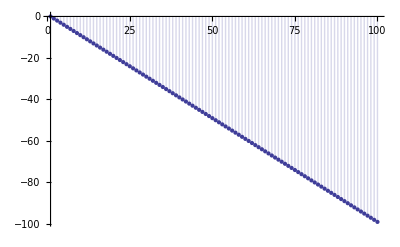

```mathematica
DiscretePlot[ N[D[LaguerreL[-1-z,1,(1-s) Log[n]] Log[n],z]/.{s->0,z->0}],{n,1,100}]
```

```mathematica
FullSimplify[Integrate[ (x)^-s, {x,1,n}]]
```

ConditionalExpression[(n^-s (-n+n^s))/(-1+s),Re[n]≥0||n∉Reals]

```mathematica
Gamma[1,0,(s-1)Log[n]]/Gamma[1]
```

1-n^(1-s)

```mathematica
Sum[ (-1)^k/(k!) Binomial[ -z,k] (Log[x])^k,{k,0,Infinity}]
```

Hypergeometric1F1[z,1,Log[x]]

```mathematica
Hypergeometric1F1[3,1,Log[100.]]
```

2081.41

```mathematica
LaguerreL[-3,Log[100.]]
```

2081.41

```mathematica
Table[Expand[ (Log[x]+Log[y])^k],{k,1,6}]//TableForm
```

Log[x]+Log[y]
Log[x]^2+2 Log[x] Log[y]+Log[y]^2
Log[x]^3+3 Log[x]^2 Log[y]+3 Log[x] Log[y]^2+Log[y]^3
Log[x]^4+4 Log[x]^3 Log[y]+6 Log[x]^2 Log[y]^2+4 Log[x] Log[y]^3+Log[y]^4
Log[x]^5+5 Log[x]^4 Log[y]+10 Log[x]^3 Log[y]^2+10 Log[x]^2 Log[y]^3+5 Log[x] Log[y]^4+Log[y]^5
Log[x]^6+6 Log[x]^5 Log[y]+15 Log[x]^4 Log[y]^2+20 Log[x]^3 Log[y]^3+15 Log[x]^2 Log[y]^4+6 Log[x] Log[y]^5+Log[y]^6

```mathematica
Grid@Table[(-1)^k / (k!) bins[-z,k] Log[x]^j Log[y]^(k-j), {k,0,5},{j,0,k}]
```

bins[-z,0] |  |  |  |  | 
-bins[-z,1] Log[y] | -bins[-z,1] Log[x] |  |  |  | 
1/2 bins[-z,2] Log[y]^2 | 1/2 bins[-z,2] Log[x] Log[y] | 1/2 bins[-z,2] Log[x]^2 |  |  | 
-1/6 bins[-z,3] Log[y]^3 | -1/6 bins[-z,3] Log[x] Log[y]^2 | -1/6 bins[-z,3] Log[x]^2 Log[y] | -1/6 bins[-z,3] Log[x]^3 |  | 
1/24 bins[-z,4] Log[y]^4 | 1/24 bins[-z,4] Log[x] Log[y]^3 | 1/24 bins[-z,4] Log[x]^2 Log[y]^2 | 1/24 bins[-z,4] Log[x]^3 Log[y] | 1/24 bins[-z,4] Log[x]^4 | 
-1/120 bins[-z,5] Log[y]^5 | -1/120 bins[-z,5] Log[x] Log[y]^4 | -1/120 bins[-z,5] Log[x]^2 Log[y]^3 | -1/120 bins[-z,5] Log[x]^3 Log[y]^2 | -1/120 bins[-z,5] Log[x]^4 Log[y] | -1/120 bins[-z,5] Log[x]^5

```mathematica
Sum[ (-1)^k/(k!)2^k  Binomial[ -z,k] (Log[x])^k,{k,0,Infinity}]
```

Hypergeometric1F1[z,1,2 Log[x]]

```mathematica
Sum[ (Log[n])^(2 k) / ((2 k)! (2 k)),{k,1,Infinity}]
```

-EulerGamma+CoshIntegral[Log[n]]-Log[Log[n]]

```mathematica
(LogIntegral[ 33.]-Log[Log[33.]]-EulerGamma)-2SinhIntegral[Log[33.]]
```

-1.83598

```mathematica
Re[(LogIntegral[1/33.]-Log[Log[1/33.]]-EulerGamma)]
```

-1.83598

```mathematica
N@LogIntegral[ 1/(33 Log[33])]-Log[Log[ 1/(33 Log[33])]]-EulerGamma
```

-2.13654-3.14159 ⅈ

```mathematica
LogIntegral[33.]-Log[Log[33.]]-EulerGamma
```

12.0634

```mathematica
FullSimplify[ (1/Log[n])(1-1/n)]
```

(-1+n)/(n Log[n])

```mathematica
Log[n-1]-Log[n]-Log[Log[n]]/.n->12
```

Log[11]-Log[12]-Log[Log[12]]

```mathematica
ss[n_, x_] := Sum[ (x^k-1)/k,{k,1,Log[x,n]}]
ss2a[n_, x_] :=Sum[ (x^k-1)/k,{k,1,2Log[x,n]}]
ss2[n_, x_] := Sum[ (x^k-1)/k,{k,Floor[Log[x,n]],2Log[x,n]}]
```

```mathematica
ss[100,1.00001]+ss2[100,1.00001]
```

1243.34

```mathematica
LogIntegral[100.]-Log@Log@100.-EulerGamma
```

28.0217

```mathematica
ss[100,1.00001]
ss2[100,1.00001]
```

28.0218

1215.32

```mathematica
LogIntegral[10000.]-Log@Log@10000.-EulerGamma
```

1243.34

```mathematica
FullSimplify[x^k + (x+c)^k]
```

x^k+(c+x)^k

```mathematica
ss2[100,1.001]
```

1214.86

```mathematica
D[Sum[Binomial[z,k] 1/(s-1)^k Gamma[k,0,(s-1)Log[n]]/Gamma[k],{k,1,Infinity}],n]
```

```mathematica
n^-s z Hypergeometric1F1[1-z,2,-Log[n]]/.s->0
```

```mathematica
Integrate[ z Hypergeometric1F1[1-z,2,-Log[n]],{n,0,x}]
```

ConditionalExpression[LaguerreL[-z,Log[x]],Re[z]>0]

```mathematica
Integrate[n z Hypergeometric1F1[1-z,2,-Log[n]],{n,0,x}]
```

∫_0^x n z Hypergeometric1F1[1-z,2,-Log[n]]ⅆn

```mathematica
Limit[(a-1)^s (-1)^s Sum[ a^k k^(s-1),{k,1,Log[a,n]}]/.{n->100,s->7/2},a->1]
```

```mathematica
N[-ⅈ (-1+a)^(7/2) (-100 a LerchPhi[a,-5/2,1+Log[100]/Log[a]]+PolyLog[-5/2,a])/.a->1.000001]
```

2.60253×10^-10-2782.57 ⅈ

```mathematica
N[6-6 n+6 n Log[n]-3 n Log[n]^2+n Log[n]^3/.n->100]
```

5573.28

```mathematica
Chop@Gamma[3.5,0,-Log[100.]]
```

0.-2782.56 ⅈ

```mathematica
N@Sum[ Re[n^k/( k! k)]/.{n->Log[12000],z->5.5},{k,1,25}]
```

1458.28

```mathematica
gg[n_, k_] := If[ k==0, Limit[ Gamma[kk,0,-Log[n]]/Gamma[kk],kk->k], Gamma[k,0,-Log[n]]/Gamma[k]]
N@Sum[ Re[(-1)^k(-1)^(k+1)/k gg[n,k]/.{n->12000,z->5}],{k,1,40}]
```

1458.28

```mathematica
FullSimplify[D[(-1)^k 1/(k!) Binomial[-z,k],z]n^k ]
```

((-1)^k n^k Binomial[-z,k] (HarmonicNumber[-k-z]-HarmonicNumber[-z]))/(k!)

```mathematica
Limit[ ((-1)^kk Gamma[kk,0,-Log[100]]/Gamma[kk]-1)/kk,kk->0]
```

ⅈ π-Gamma[0,-Log[100]]

```mathematica
pp[ n_, z_] := (((-1)^z  Gamma[z,0,-Log[n]]/Gamma[z])-((-1)^-z  Gamma[-z,0,-Log[n]]/Gamma[-z]))/(2z)
pp2[ n_, z_] := (((-1)^z  Gamma[z,0,-Log[n]]/Gamma[z])-1)/z
```

```mathematica
pp[100,.000001]
```

30.1261+6.28319 ⅈ

```mathematica
D[ LogIntegral[n]-Log@Log@n-EulerGamma,n]
```

1/Log[n]-1/(n Log[n])

```mathematica
N[D[ LaguerreL[-z,Log[n]],n]/.{n->100,z->3}]
```

27.4193

```mathematica
-N@Sum[ (-1)^i Binomial[ -z-1+1, -z-1-i]Log[ n]^i / i!, {i,0,-z-1}]/n/.{z->3,n->100}
```

27.4193

```mathematica
D[ LaguerreL[-z,Log[n]],n]
```

-LaguerreL[-1-z,1,Log[n]]/n

```mathematica
Sum[ (-1)^i Binomial[ -z-1+1, -z-1-i]Log[ n]^i / i!, {i,0,-z-1}]/n
```

-(z Hypergeometric1F1[1+z,2,Log[n]])/n

```mathematica
D[(-1)^z,z]
```

ⅈ (-1)^z π

```mathematica
FullSimplify@D[(-1)^z Gamma[z,0,-Log[n]]/Gamma[z],z]
```

$Aborted

```mathematica
-N@Gamma[0, -Log[100]]
```

30.1261+3.14159 ⅈ

```mathematica
D[ LogIntegral[n]-Log@Log@n - EulerGamma,n]
```

1/Log[n]-1/(n Log[n])

```mathematica
D[LogIntegral[n]-Log@Log@n - EulerGamma,n]/.n->20
```

19/(20 Log[20])

```mathematica
FullSimplify@(1/Log[n])(1-1/n)/.n->20
```

19/(20 Log[20])

```mathematica
Limit[ (1/Log[x])(1-1/x),x->1]
```

1

```mathematica
Limit[ 1/Log[x],x->1]
```

∞

```mathematica
Expand[(1/Log[x])(1-1/x)]
```

1/Log[x]-1/(x Log[x])

```mathematica
D[ 1/Log[x],x]
```

-1/(x Log[x]^2)

```mathematica
D[ 1-1/x,x]
```

1/x^2

```mathematica
LogIntegral[1]
```

-∞

```mathematica
Limit[ LogIntegral[ 1+x]/x, x->0]
```

-∞

```mathematica
Integrate[ (x-1)/( Log[x]),x]
```

ExpIntegralEi[2 Log[x]]-LogIntegral[x]

```mathematica
N@ExpIntegralEi[2 Log[x]]-LogIntegral[x]/.x->10
```

23.9605

```mathematica
N@LogIntegral[ 100]-LogIntegral[10]
```

23.9605

```mathematica
Integrate[ (1-1/x)(x^(-1))/( Log[x]),x]
```

-ExpIntegralEi[-Log[x]]+Log[Log[x]]

```mathematica
N@ExpIntegralEi[3 Log[x]]/.x->30
```

2984.42

```mathematica
N@Log@Log@30 - N@LogIntegral[ 30^-1]
```

1.23201

```mathematica
N@Integrate[ (1-1/x)(x^z/ Log[x]),x]
```

-1. ExpIntegralEi[z Log[x]]+ExpIntegralEi[(1.+z) Log[x]]

```mathematica
Integrate[ x^z/Log[x],x]
```

ExpIntegralEi[(1+z) Log[x]]

```mathematica
Integrate[ 1-1/x,x]
```

x-Log[x]

```mathematica
Expand[ ( 1-1/x)(x^z/Log[x]),x]
```

-x^(-1+z)/Log[x]+x^z/Log[x]

```mathematica
Limit[ LogIntegral[x^5]-Log[Log[x]],x->1]
```

EulerGamma+Log[5]

```mathematica
Limit[ LogIntegral[x^2]-LogIntegral[x],x->1]
```

Log[2]

```mathematica
Limit[ LogIntegral[x^2]-LogIntegral[x^-2],x->1]
```

0

```mathematica
Limit[ LogIntegral[x^5]-LogIntegral[x^-2],x->1]
```

Log[5/2]

```mathematica
Limit[ LogIntegral[x^5]-LogIntegral[x^3],x->1]
```

Log[5/3]

```mathematica
Limit[ LogIntegral[x^6]-LogIntegral[x^(1/10)],x->1]
```

Log[60]

```mathematica
Limit[ LogIntegral[x^2]-Log[Log[x]],x->1]
```

EulerGamma+Log[2]

```mathematica
Integrate[ x^-1/Log[x],x]
```

Log[Log[x]]

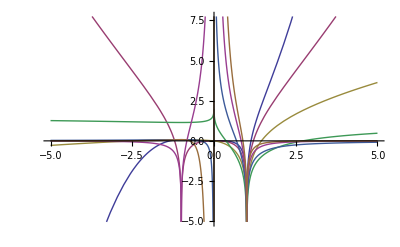

```mathematica
Plot[{Re@ LogIntegral[x^3],Re@ LogIntegral[x^2],Re@ LogIntegral[x], Re@ Log[Log[x]],Re@ LogIntegral[x^-1], Re@ LogIntegral[x^-2], Re@ LogIntegral[x^-3]},{x,-5,5}]
```

```mathematica
D[LogIntegral[x^s],x]
```

(s x^(-1+s))/Log[x^s]

```mathematica
Limit[(s x^(-1+s))/Log[x^s], s->0]
```

1/(x Log[x])

```mathematica
Integrate[ 1/(x Log[x]),x]
```

Log[Log[x]]

```mathematica
Animate[ Plot[{Re@ LogIntegral[x^y]},{x,29,31}], {y,-1,1}]
```

```mathematica
Limit[ LogIntegral[x^z],z->.000000001]/.x->30
```

-18.9219

```mathematica
Integrate[ (s x^(-1+s))/Log[x^s], x]
```

LogIntegral[x^s]

```mathematica
Limit[(s x^(-1+s))/Log[x^s],x->1]
```

s DirectedInfinity[1/Sign[s]]

```mathematica
(s x^(-1+s))/(s Log[x])
```

```mathematica
Integrate[ x^(-1+s)/Log[x],x]
```

ExpIntegralEi[s Log[x]]

```mathematica
Limit[ x^(-1+s)/Log[x],x->1]
```

∞

```mathematica
Integrate[x^-1/( Log[x]),x]
```

Log[Log[x]]

```mathematica
Integrate[ x^(s-1),x]
```

x^s/s

```mathematica
D[LogIntegral[x^s],x]
```

(s x^(-1+s))/Log[x^s]

```mathematica
Integrate[ x^(s) x^(t),x]
```

x^(1+s+t)/(1+s+t)

```mathematica
Expand[Integrate[ (x^(s-1)/Log[x]) (x^(t-1)/Log[x]),{x,0,20}, PrincipalValue->True]]/.{s->4,t->4}
```

Integrate::idiv: Integral of x^6/Log[x]^2 does not converge on {0, 20}.

Integrate[x^6/Log[x]^2,{x,0,20},PrincipalValue→True]

```mathematica
N[LogIntegral[x^4]LogIntegral[x^4]/.x->20]
```

2.16967×10^8

```mathematica
N[7 ExpIntegralEi[7 Log[x]]-x^7/Log[x]]/.x->20
```

2.26681×10^7

```mathematica
Expand[Integrate[ (x^(s-1)/Log[x]),x]]/.{s->4}
```

ExpIntegralEi[4 Log[x]]

```mathematica
N[LogIntegral[x^4]/.x->20]
```

14729.8

```mathematica
N[ExpIntegralEi[4 Log[x]]/.x->20]
```

14729.8

```mathematica
7 ExpIntegralEi[7 Log[x]]-x^7/Log[x]/.x->1
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ComplexInfinity + -∞ encountered.

Indeterminate

```mathematica
FullSimplify@Integrate[ x^(s-1) /Log[x^2],x]
```

1/2 x^s (x^2)^(-s/2) ExpIntegralEi[1/2 s Log[x^2]]

```mathematica
N[1/2 x^s (x^2)^(-s/2) ExpIntegralEi[1/2 s Log[x^2]]/.{x->100,s->1}]
```

15.0631

```mathematica
N[1/2 x^s (x^2)^(-s/2) LogIntegral[x^s]/.{x->100,s->2}]
```

623.069

```mathematica
N[1/2 LogIntegral[x^s]/.{x->100,s->2}]
```

623.069

```mathematica
N[1/2 x^s (x^2)^(-s/2) ExpIntegralEi[1/2 s Log[x^2]]/.{x->30,s->3}]
```

1492.21

```mathematica
N@LogIntegral[30^3]/2
```

1492.21

```mathematica
FullSimplify@Integrate[ x^(s-1) /Log[x^3],x]
```

1/3 x^s (x^3)^(-s/3) ExpIntegralEi[1/3 s Log[x^3]]

```mathematica
N[1/3 x^s (x^3)^(-s/3) ExpIntegralEi[1/3 s Log[x^3]]/.{x->40,s->4}]
```

62438.2

```mathematica
N@LogIntegral[40^4]/3
```

62438.2

```mathematica
Integrate[ x^(-1)  Log[x]^k,x]
```

Log[x]^(1+k)/(1+k)

```mathematica
LogIntegral[ x^s]/k
```

```mathematica
Integrate[ x^-1 Log[x]^-1,x]
```

Log[Log[x]]

```mathematica
Integrate[ LogIntegral[x],x]
```

-ExpIntegralEi[2 Log[x]]+x LogIntegral[x]

```mathematica
Integrate[ LogIntegral[x^2],x]/.x->10
```

-ExpIntegralEi[(3 Log[100])/2]+10 LogIntegral[100]

```mathematica
Integrate[ LogIntegral[x^3],x]/.x->10
```

-ExpIntegralEi[(4 Log[1000])/3]+10 LogIntegral[1000]

```mathematica
Integrate[Log[Log[x]],x]
```

x Log[Log[x]]-LogIntegral[x]

```mathematica
Integrate[ LogIntegral[x^(1/500)],{x,0,1}]
```

-Log[501]

```mathematica
Integrate[ Log[Log[x]],{x,0,1}]
```

-EulerGamma+ⅈ π

```mathematica
Integrate[Log[x],{x,0,1}]
```

-1

```mathematica
p[n_,k_]=Sum[1/k-p[n/j,k-1],{j,2,k}]
p[100,1]
```

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of $IterationLimit :: itlim will be suppressed during this calculation.

```mathematica
D[ n!,n]
```

Gamma[1+n] PolyGamma[0,1+n]

```mathematica
Grid[Table[ Integrate[ x^(s-1)/(Log[x]^k),x], {k,-4,4},{s,-4,4}]]
```

-3/(128 x^4)-(3 Log[x])/(32 x^4)-(3 Log[x]^2)/(16 x^4)-Log[x]^3/(4 x^4)-Log[x]^4/(4 x^4) | -8/(81 x^3)-(8 Log[x])/(27 x^3)-(4 Log[x]^2)/(9 x^3)-(4 Log[x]^3)/(9 x^3)-Log[x]^4/(3 x^3) | -3/(4 x^2)-(3 Log[x])/(2 x^2)-(3 Log[x]^2)/(2 x^2)-Log[x]^3/x^2-Log[x]^4/(2 x^2) | -24/x-(24 Log[x])/x-(12 Log[x]^2)/x-(4 Log[x]^3)/x-Log[x]^4/x | Log[x]^5/5 | 24 x-24 x Log[x]+12 x Log[x]^2-4 x Log[x]^3+x Log[x]^4 | (3 x^2)/4-3/2 x^2 Log[x]+3/2 x^2 Log[x]^2-x^2 Log[x]^3+1/2 x^2 Log[x]^4 | (8 x^3)/81-8/27 x^3 Log[x]+4/9 x^3 Log[x]^2-4/9 x^3 Log[x]^3+1/3 x^3 Log[x]^4 | (3 x^4)/128-3/32 x^4 Log[x]+3/16 x^4 Log[x]^2-1/4 x^4 Log[x]^3+1/4 x^4 Log[x]^4
-3/(128 x^4)-(3 Log[x])/(32 x^4)-(3 Log[x]^2)/(16 x^4)-Log[x]^3/(4 x^4) | -2/(27 x^3)-(2 Log[x])/(9 x^3)-Log[x]^2/(3 x^3)-Log[x]^3/(3 x^3) | -3/(8 x^2)-(3 Log[x])/(4 x^2)-(3 Log[x]^2)/(4 x^2)-Log[x]^3/(2 x^2) | -6/x-(6 Log[x])/x-(3 Log[x]^2)/x-Log[x]^3/x | Log[x]^4/4 | -6 x+6 x Log[x]-3 x Log[x]^2+x Log[x]^3 | -(3 x^2)/8+3/4 x^2 Log[x]-3/4 x^2 Log[x]^2+1/2 x^2 Log[x]^3 | -(2 x^3)/27+2/9 x^3 Log[x]-1/3 x^3 Log[x]^2+1/3 x^3 Log[x]^3 | -(3 x^4)/128+3/32 x^4 Log[x]-3/16 x^4 Log[x]^2+1/4 x^4 Log[x]^3
-1/(32 x^4)-Log[x]/(8 x^4)-Log[x]^2/(4 x^4) | -2/(27 x^3)-(2 Log[x])/(9 x^3)-Log[x]^2/(3 x^3) | -1/(4 x^2)-Log[x]/(2 x^2)-Log[x]^2/(2 x^2) | -2/x-(2 Log[x])/x-Log[x]^2/x | Log[x]^3/3 | 2 x-2 x Log[x]+x Log[x]^2 | x^2/4-1/2 x^2 Log[x]+1/2 x^2 Log[x]^2 | (2 x^3)/27-2/9 x^3 Log[x]+1/3 x^3 Log[x]^2 | x^4/32-1/8 x^4 Log[x]+1/4 x^4 Log[x]^2
-1/(16 x^4)-Log[x]/(4 x^4) | -1/(9 x^3)-Log[x]/(3 x^3) | -1/(4 x^2)-Log[x]/(2 x^2) | -1/x-Log[x]/x | Log[x]^2/2 | -x+x Log[x] | -x^2/4+1/2 x^2 Log[x] | -x^3/9+1/3 x^3 Log[x] | -x^4/16+1/4 x^4 Log[x]
-1/(4 x^4) | -1/(3 x^3) | -1/(2 x^2) | -1/x | Log[x] | x | x^2/2 | x^3/3 | x^4/4
ExpIntegralEi[-4 Log[x]] | ExpIntegralEi[-3 Log[x]] | ExpIntegralEi[-2 Log[x]] | ExpIntegralEi[-Log[x]] | Log[Log[x]] | LogIntegral[x] | ExpIntegralEi[2 Log[x]] | ExpIntegralEi[3 Log[x]] | ExpIntegralEi[4 Log[x]]
-4 ExpIntegralEi[-4 Log[x]]-1/(x^4 Log[x]) | -3 ExpIntegralEi[-3 Log[x]]-1/(x^3 Log[x]) | -2 ExpIntegralEi[-2 Log[x]]-1/(x^2 Log[x]) | -ExpIntegralEi[-Log[x]]-1/(x Log[x]) | -1/Log[x] | -x/Log[x]+LogIntegral[x] | 2 ExpIntegralEi[2 Log[x]]-x^2/Log[x] | 3 ExpIntegralEi[3 Log[x]]-x^3/Log[x] | 4 ExpIntegralEi[4 Log[x]]-x^4/Log[x]
8 ExpIntegralEi[-4 Log[x]]-1/(2 x^4 Log[x]^2)+2/(x^4 Log[x]) | 9/2 ExpIntegralEi[-3 Log[x]]-1/(2 x^3 Log[x]^2)+3/(2 x^3 Log[x]) | 2 ExpIntegralEi[-2 Log[x]]-1/(2 x^2 Log[x]^2)+1/(x^2 Log[x]) | 1/2 ExpIntegralEi[-Log[x]]-1/(2 x Log[x]^2)+1/(2 x Log[x]) | -1/(2 Log[x]^2) | -x/(2 Log[x]^2)-x/(2 Log[x])+LogIntegral[x]/2 | 2 ExpIntegralEi[2 Log[x]]-x^2/(2 Log[x]^2)-x^2/Log[x] | 9/2 ExpIntegralEi[3 Log[x]]-x^3/(2 Log[x]^2)-(3 x^3)/(2 Log[x]) | 8 ExpIntegralEi[4 Log[x]]-x^4/(2 Log[x]^2)-(2 x^4)/Log[x]
-32/3 ExpIntegralEi[-4 Log[x]]-1/(3 x^4 Log[x]^3)+2/(3 x^4 Log[x]^2)-8/(3 x^4 Log[x]) | -9/2 ExpIntegralEi[-3 Log[x]]-1/(3 x^3 Log[x]^3)+1/(2 x^3 Log[x]^2)-3/(2 x^3 Log[x]) | -4/3 ExpIntegralEi[-2 Log[x]]-1/(3 x^2 Log[x]^3)+1/(3 x^2 Log[x]^2)-2/(3 x^2 Log[x]) | -1/6 ExpIntegralEi[-Log[x]]-1/(3 x Log[x]^3)+1/(6 x Log[x]^2)-1/(6 x Log[x]) | -1/(3 Log[x]^3) | -x/(3 Log[x]^3)-x/(6 Log[x]^2)-x/(6 Log[x])+LogIntegral[x]/6 | 4/3 ExpIntegralEi[2 Log[x]]-x^2/(3 Log[x]^3)-x^2/(3 Log[x]^2)-(2 x^2)/(3 Log[x]) | 9/2 ExpIntegralEi[3 Log[x]]-x^3/(3 Log[x]^3)-x^3/(2 Log[x]^2)-(3 x^3)/(2 Log[x]) | 32/3 ExpIntegralEi[4 Log[x]]-x^4/(3 Log[x]^3)-(2 x^4)/(3 Log[x]^2)-(8 x^4)/(3 Log[x])

```mathematica
Integrate[ x^(s-1) (Log[x]^k),x]/.{s->1,x->10}
```

-(-1)^(-1-k) Gamma[1+k,-Log[10]]

```mathematica
Log[x]^(1+k) (-s Log[x])^(-1-k)/.x->30
```

(-s)^(-1-k)

```mathematica
Table[(-1)^k,{k,-4,4}]
```

{1,-1,1,-1,1,-1,1,-1,1}

```mathematica
-(-s)^(-1+k)Gamma[1-k,-s Log[x]]
```

-(-s)^(-1+k) Gamma[1-k,-s Log[x]]

```mathematica
(-1)^k Gamma[1+k,-Log[x]]
```

(-1)^k Gamma[1+k,-Log[x]]

```mathematica
Integrate[1/  (Log[x]^k),x]/.{x->20}
```

(-1)^k Gamma[1-k,-Log[20]]

```mathematica
Limit[ (-1)^(k) Integrate[(Log[x]^(k)),x],x->1]
```

Gamma[1+k,0]

```mathematica
N@Gamma[5,-Log[1.01]]
```

24.-1.20448×10^-26 ⅈ

```mathematica
(4.5+I)!
```

-2.21893+47.3558 ⅈ

```mathematica
Limit[  Integrate[(-1)^k(Log[x]^k),x],x->1]/.k->7
```

5040

```mathematica
-Integrate[(Log[1/x]^k),{x,1,n}]
```

ConditionalExpression[Gamma[1+k]-Gamma[1+k,-Log[n]],Re[k]>-1&&Log[n]>0]

```mathematica
N[-Integrate[(Log[1/x]^3),{x,1,n}]/.n->100]
```

5573.28

```mathematica
Chop@Gamma[4,0,-Log[100.]]
```

5573.28

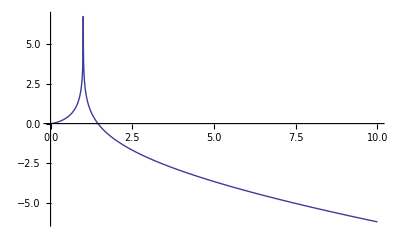

```mathematica
Plot[-ExpIntegralEi[-Log[1/x]],{x,0,10}]
```

```mathematica
Integrate[1/Log[1/x],x]
```

-ExpIntegralEi[-Log[1/x]]

```mathematica
Expand@Integrate[ Log[x],{x,1,n}]
```

ConditionalExpression[1-n+n Log[n],Re[n]≥0||n∉Reals]

```mathematica
FullSimplify@Integrate[ Log[x]^z,{x,1,n}]
```

ConditionalExpression[(-z Gamma[z]+Gamma[1+z,-Log[n]]) (-Log[n])^-z Log[n]^z,Re[z]>-1]

```mathematica
FullSimplify@Integrate[ (1/x)^z,{x,1,n}]
```

ConditionalExpression[-(-1+(1/n)^(-1+z))/(-1+z),Re[n]≥0||n∉Reals]

```mathematica
(-z Gamma[z]+Gamma[1+z,-Log[n]]) (-Log[n])^-z Log[n]^z/.n->100
```

(-1)^-z (-z Gamma[z]+Gamma[1+z,-Log[100]])

```mathematica
FullSimplify[-(-1+(1/n)^(-1+z))/(-1+z)]/.n->200
```

-(-1+200^(1-z))/(-1+z)

```mathematica
Integrate[ Log[1/x]^z,x]
```

Gamma[1+z,Log[1/x]]

```mathematica
Integrate[ x^-1 Log[x]^-1,x]
```

Log[Log[x]]

```mathematica
Integrate[ x^(s-1)Log[x]^(k-1),x]/.{x->10}
```

-(-s)^-k Gamma[k,-s Log[10]]

```mathematica
Integrate[ 1/(x Log[x]),x]
```

Log[Log[x]]

```mathematica
Integrate[ x^(k-1) (E^x)^(s),x]
```

-ⅇ^(-s x) (ⅇ^x)^s x^k (-s x)^-k Gamma[k,-s x]

```mathematica
FullSimplify[-ⅇ^(-s x) (ⅇ^x)^s x^k (-s x)^-k Gamma[k,-s x]/.x->10]
```

-(-s)^-k Gamma[k,-10 s]

```mathematica
Integrate[ (E^x)^(0)x^(0-1) ,x]
```

Log[x]

```mathematica
-ⅇ^(-s x) (ⅇ^x)^s x^k (-s x)^-k Gamma[k,-s x]/.s->-1
```

-Gamma[k,x]

```mathematica
Limit[ -Gamma[k,x]+Gamma[k,0],x->Infinity]/.k->8
```

5040

```mathematica
Integrate[ x^-2 Log[ x]^(k-1),{x,1,Infinity}]
```

ConditionalExpression[Gamma[k],Re[k]>0]

```mathematica
Integrate[  (-Log[ x])^k/(x^2),{x,1,n}]
```

ConditionalExpression[(-1)^k (Gamma[1+k]-Gamma[1+k,Log[n]]),Re[k]>-1&&Log[n]>0]

```mathematica
Integrate[ (Log[x]^(k-1)/x^2) (Log[y])^(-k)/(y^2),{x,1,Infinity},{y,1,Infinity}]
```

ConditionalExpression[Gamma[1-k] Gamma[k],Re[k]>0]

```mathematica
Pi/Sin[ Pi 3.2]
```

-5.3448

```mathematica
Expand[(Log[x]^(k-1)/x^2) (Log[y])^(-k)/(y^2)]
```

(Log[x]^(-1+k) Log[y]^-k)/(x^2 y^2)

```mathematica
Integrate[ Log[x]^k/x^2,{x,1,Infinity}]
```

ConditionalExpression[Gamma[1+k],Re[k]>-1]

```mathematica
Integrate[ (E^x)^s x^(k-1),x]/.x->10
```

-(-s)^-k Gamma[k,-10 s]

```mathematica
Grid[Table[Expand@Integrate[ x^(s-1) Log[x]^(k-1),x],{k,-2,2},{s,-2,2}]]
```

2 ExpIntegralEi[-2 Log[x]]-1/(2 x^2 Log[x]^2)+1/(x^2 Log[x]) | 1/2 ExpIntegralEi[-Log[x]]-1/(2 x Log[x]^2)+1/(2 x Log[x]) | -1/(2 Log[x]^2) | -x/(2 Log[x]^2)-x/(2 Log[x])+LogIntegral[x]/2 | 2 ExpIntegralEi[2 Log[x]]-x^2/(2 Log[x]^2)-x^2/Log[x]
-2 ExpIntegralEi[-2 Log[x]]-1/(x^2 Log[x]) | -ExpIntegralEi[-Log[x]]-1/(x Log[x]) | -1/Log[x] | -x/Log[x]+LogIntegral[x] | 2 ExpIntegralEi[2 Log[x]]-x^2/Log[x]
ExpIntegralEi[-2 Log[x]] | ExpIntegralEi[-Log[x]] | Log[Log[x]] | LogIntegral[x] | ExpIntegralEi[2 Log[x]]
-1/(2 x^2) | -1/x | Log[x] | x | x^2/2
-1/(4 x^2)-Log[x]/(2 x^2) | -1/x-Log[x]/x | Log[x]^2/2 | -x+x Log[x] | -x^2/4+1/2 x^2 Log[x]

```mathematica
Grid[Table[Expand@Integrate[ (E^x)^s x^(k-1),x],{k,-2,2},{s,-2,2}]]
```

-ⅇ^(-2 x)/(2 x^2)+ⅇ^(-2 x)/x+2 ExpIntegralEi[-2 x] | -ⅇ^-x/(2 x^2)+ⅇ^-x/(2 x)+ExpIntegralEi[-x]/2 | -1/(2 x^2) | -ⅇ^x/(2 x^2)-ⅇ^x/(2 x)+ExpIntegralEi[x]/2 | -ⅇ^(2 x)/(2 x^2)-ⅇ^(2 x)/x+2 ExpIntegralEi[2 x]
-ⅇ^(-2 x)/x-2 ExpIntegralEi[-2 x] | -ⅇ^-x/x-ExpIntegralEi[-x] | -1/x | -ⅇ^x/x+ExpIntegralEi[x] | -ⅇ^(2 x)/x+2 ExpIntegralEi[2 x]
ExpIntegralEi[-2 x] | ExpIntegralEi[-x] | Log[x] | ExpIntegralEi[x] | ExpIntegralEi[2 x]
-1/2 ⅇ^(-2 x) | -ⅇ^-x | x | ⅇ^x | ⅇ^(2 x)/2
-1/4 ⅇ^(-2 x)-1/2 ⅇ^(-2 x) x | -ⅇ^-x-ⅇ^-x x | x^2/2 | -ⅇ^x+ⅇ^x x | -ⅇ^(2 x)/4+1/2 ⅇ^(2 x) x

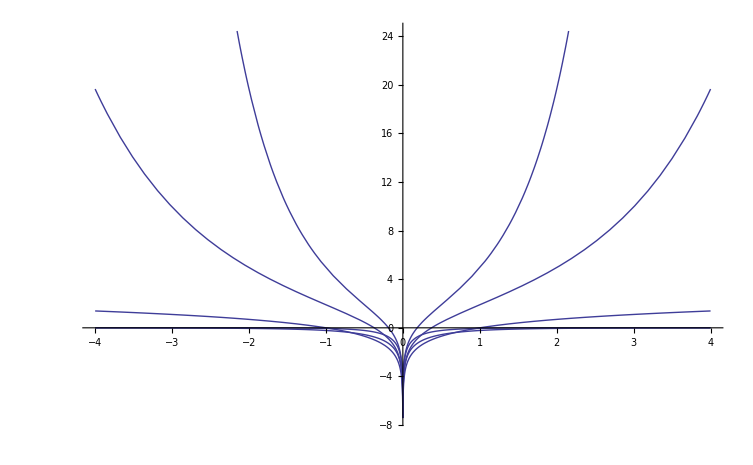

```mathematica
Plot[Re[{ExpIntegralEi[-2 x],ExpIntegralEi[-x],Log[x],ExpIntegralEi[x],ExpIntegralEi[2 x]}],{x,-4,4}]
```

```mathematica
Grid[Table[Integrate[ x^(s-1) Log[x]^(k-1),{x,1,Infinity}],{k,1,6},{s,-6,-1}]]
```

1/6 | 1/5 | 1/4 | 1/3 | 1/2 | 1
1/36 | 1/25 | 1/16 | 1/9 | 1/4 | 1
1/108 | 2/125 | 1/32 | 2/27 | 1/4 | 2
1/216 | 6/625 | 3/128 | 2/27 | 3/8 | 6
1/324 | 24/3125 | 3/128 | 8/81 | 3/4 | 24
5/1944 | 24/3125 | 15/512 | 40/243 | 15/8 | 120

```mathematica
Grid[Table[Gamma[k](-s)^-k,{k,1,6},{s,-6,-1}]]
```

1/6 | 1/5 | 1/4 | 1/3 | 1/2 | 1
1/36 | 1/25 | 1/16 | 1/9 | 1/4 | 1
1/108 | 2/125 | 1/32 | 2/27 | 1/4 | 2
1/216 | 6/625 | 3/128 | 2/27 | 3/8 | 6
1/324 | 24/3125 | 3/128 | 8/81 | 3/4 | 24
5/1944 | 24/3125 | 15/512 | 40/243 | 15/8 | 120

```mathematica
Integrate[ x^(s-1) Log[x]^(k-1),{x,1,Infinity}]
```

ConditionalExpression[(-s)^-k Gamma[k],Re[s]<0&&Re[k]>0]

```mathematica
Integrate[ Log[x]^z,{x,1,n}]
```

ConditionalExpression[(-z Gamma[z]+Gamma[1+z,-Log[n]]) (-Log[n])^-z Log[n]^z,Re[z]>-1]

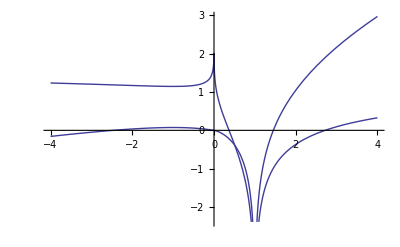

```mathematica
Plot[Re[{Log@Log@x,LogIntegral[x]}],{x,-4,4}]
```

```mathematica
FullSimplify@D[-(-s)^-k Gamma[k,-s Log[x]],k]
```

(-s)^-k (Gamma[k,-s Log[x]] (Log[-s]-Log[-s Log[x]])-MeijerG[{{},{1,1}},{{0,0,k},{}},-s Log[x]])

```mathematica
FullSimplify@D[-(-s)^-k Gamma[k,-s x],k]
```

(-s)^-k (Gamma[k,-s x] (Log[-s]-Log[-s x])-MeijerG[{{},{1,1}},{{0,0,k},{}},-s x])

```mathematica
-Integrate[Log[1/x]^(z-1) x^(s-1),{x,1,n}]
```

ConditionalExpression[-(-1)^z (-s)^-z (-Gamma[z]+Gamma[z,-s Log[n]]),Re[z]>0&&Log[n]>0]

```mathematica
FullSimplify[(-1)^z (-s)^-z]/.z->-4
```

s^4

```mathematica
s^-z Gamma[z,0,-s Log[n]]
```

s^-z Gamma[z,0,-s Log[n]]

```mathematica
-Integrate[(-Log[x])^(z-1) x^(s-1),{x,1,n}]
```

ConditionalExpression[-(-1)^z (-s)^-z (-Gamma[z]+Gamma[z,-s Log[n]]),Re[z]>0&&Log[n]>0]

```mathematica
N[-(-1)^z (-s)^-z (-Gamma[z]+Gamma[z,-s Log[n]])/.{n->10,z->2,s->2}]
```

90.3793-1.10377×10^-14 ⅈ

```mathematica
N[-Integrate[(-Log[x])^(z-1) x^(s-1),{x,1,n}]/.{n->10,z->2,s->2}]
```

90.3793-1.10377×10^-14 ⅈ

```mathematica
N[s^-z (Gamma[z,0,-s Log[n]])/.{n->10,z->2,s->2}]
```

90.3793-1.10377×10^-14 ⅈ